# Empirical Analysis of P vs. NP: On the Equivalence of Turing Machines as Partial Functions

Michael Sun

Wolfram High School Summer Research Program 2025
Edited 28 September, 2025

A Turing machine is a theoretical model of computation classified as an automaton invented by Alan Turing that operates on an infinite tape of sequential memory. The significance of Turing machines, as described in the Church-Turing thesis, comes from their ability to compute any function and therefore have the same computational ability as all conventional computers. Empirical evidence suggests that there exists Turing machines that follow different rules but ultimately compute the same function, presumably for all inputs. Naturally, these machines will have different runtimes, which models multiple computers running different algorithms to reach the same goal. Similarly, motivation for studying complexity theory comes from analyzing and improving algorithms. A central unsolved problem in the field is if quickly verifying a solution to a problem implies the existence of an algorithm that quickly solves it—commonly known as the P vs. NP problem. Analyzing patterns in the range of runtimes for equivalent Turing machines provides potential for empirically hypothesizing at the relationship between P and NP.

## Introduction

Formally, a Turing machine is a tuple of a set of states, a halt state, a set of symbols called its alphabet, and a lookup table of all possible state-symbol pairs. Turing machines keep a pointer to the cell it is currently reading, and the symbol on this cell combined with its current state defines a transition. For each transition, three operations occur: read the symbol on the current cell, write a (not necessarily distinct) symbol to the current cell, and move to an adjacent cell. Certain traits of a Turing machine are difficult to quickly represent with a real computer, so the results in this essay will be close approximations of the real behavior of Turing machines. Specifically, we will bound a finite section of the tape and set a halting condition as when the head moves left of its starting point used in S. Wolfram, A New Kind of Science. Wolfram Media, 2002 instead of the orthodox method of having a halting state.

### Terminology

In this essay, the variables  and  generally refer to the  states and  symbols of a Turing machine, and the ordered pair  refers to an -state -symbol Turing machine. Additionally, we define setting a Turing machine to a nonnegative integer  as filling our chosen interval  of the tape of length  for some  with the binary representation of  in big endian (natural left-to-right order). We ensure that the number of bits fits in  (i.e.  ). Additionally, we define the value of a Turing machine as the number created by each cell on  as base- digits where the blank symbol translates to zero. Later, we propose a slightly different way of interpreting the value.

### Formalism

Let  be the set of all -state -symbol Turing machines. Each machine in  represents a partial function ⇀ on a fixed interval  of length  on the tape where  is the set of symbols and  is the set of input symbols. For this essay, we set . Equivalently, this function can also be represented as ℕ⇀ℕ with input specified by the base k number formed on  where each symbol is an integer between 0 and . Define two Turing machines in  to be equivalent if they compute the same partial function on , or both do not exist. The number of distinct machines is then the cardinality of . For each equivalence class, we will analyze patterns of the worst-case running times of each machine in the class and over all classes in  for different  and .

For example, the following 2-state 2-symbol Turing machine takes in  where 1’s are colored orange. The output is read as . It turns out that this rule always adds 1 to the input for our constraints.

Evolution of the function  described by rule 451 for ,  input  for 5 steps:

```mathematica
RulePlot[TuringMachine[445],{{1,4},{IntegerDigits[5,2,4],0}},5,ImageSize->Small]//Rasterize
```

-Graphics-

### Theory

Only certain  pairs are capable of simulating any other Turing machine starting from a blank tape. For example, any Turing machine with one symbol trivially fails to be universal because it will not edit the tape. Pairs that can simulate all other machines are known as universal Turing machines. Additionally, weakly universal Turing machines are machines that are universal on an arbitrary initial tape. Notably, the smallest of these machines are fully analyzable within computational constraints, such as , , and Wolfram’s  machine.

The universality of Turing machines as a mathematical model of computation revealed limits of computing, notably cases of logical (un)decidability. A problem is undecidable if and only if it is provable that there exists no algorithm that will always return the correct answer to the problem. Turing’s major result was his proof of the undecidability of determining if a computer program halts, famously known as the halting problem.

#### The Halting Problem and Rice’s Theorem

The usefulness of the undecidability of the halting problem is not only limited to the statement itself, but because many problems can be shown to be undecidable by reducing them to the halting problem. More notably, it is undecidable to determine if two Turing machines are equivalent, which necessitates the mentioned constraints. Similarly, the task to quickly analyze the behavior of a Turing machine without simulating it is a generalization of the halting problem known as Rice’s theorem, which implies that this task is generally undecidable. However, it does not say anything about determining relationships between machines, which we will see in a later section could contain a predictable pattern.

## Implementation

Due to the undecidability of universal static analysis and the computational irreducibility of Turing machine evolution, the implementation will inevitably be brute-force in nature. However, there are certain ways to prune the search space by examining only the rules. There are also optimizations for Turing machine simulation, particularly with memoizing sections of the tape.

### Prune

Despite the undecidability of finding a universal way of reducing computation across Turing machines or even on one Turing machine, we can take inspiration from DFA (deterministic finite automaton) minimization. Specifically, one big optimization we can make is to declare that all Turing machines with rules that permute a dead state (unreachable from the initial state) to be equal: each of these permutations are unreachable anyway.

The diagram below shows two equivalent Turing machines, each with a different permutation of the rules from state 2, which is unreachable from state 1.

```mathematica
GraphicsRow[{
Graph[{1->1,1->1,2->1,2->1,3->1,3->1},VertexLabels->Automatic],
Graph[{1->1,1->1,2->1,2->1,3->2,3->2},VertexLabels->Automatic]
},
ImageSize->Medium
]//Rasterize
```

-Graphics-

Determining the reachable nodes reduces to graph traversal. It is not hard to see that all state graphs have  vertices and  edges, resulting in a runtime of . Building this graph is straightforward by simply inspecting the full form of the Turing machine rule.

There are two ways to describe a Turing machine rule in the Wolfram Language: full form as a list of transitions, or an index as an integer. We want to take advantage of the language’s indexing method to skip over redundant rules. Increasing the index permutes rules in the following order: direction (-1 to 1), then symbol (0 to ), then state (1 to ). Notice that if the reachable states are consecutive (which must include state 1), we can permute the rest of the states that are unreachable without changing what the TM does. For example, a 3-state TM can only reach states 1 and 2, we can permute the rules from state 3, which defines a contiguous interval of rule numbers that are equivalent (i.e. rules 83520 to 84096 for a (3,2) TM). Thus, for each of these intervals we see, we can skip ahead to the end of the interval when we detect a beginning to avoid checking redundant rules.

The length of an iteration depends on the number of reachable states. If there are  reachable states from 1 to , then there are  unreachable states. The number of ways we can permute these unreachable states is given by , since there are  symbols per state and  ways to permute each single component of a rule. Notice  is the number of s-state k-symbol Turing machines.

Returns :

```mathematica
perm=Function[{d,s,k},(2s k)^(k(s-d))];
```

There exists resource functions for converting between the two forms of a Turing machine rule, but as we will see later, these functions are too slow, so I have taken their source code and written a compiled version. We will also declare perm in our environment so it can be used in compiled functions.

Reset the compiler environment:

```mathematica
$CompilerEnvironment=CreateCompilerEnvironment[];
```

#### Compiled TuringMachineFromNumber and TuringMachineToNumber

Function functions to be compiled:

```mathematica
TuringMachineFromNumberCompiledFn=Function[{n,s,k},
With[{l=Partition[IntegerDigits[n,2 s k,s k],k]},
Module[{fa=CreateDataStructure["FixedArray",s k],it=1},
Do[Do[
fa["Part",it++]={i,k-j}->{1,1,2} Mod[Quotient[l[[i,j]],{2k,2,1}],{s,k,2}]+{1,0,-1},
{j,k}],{i,s}];
fa["Elements"]
]
]
];
```

```mathematica
TuringMachineToNumberCompiledFn=Function[{rules,s,k},
Module[{fa=CreateDataStructure["FixedArray",s k]},
Do[
fa["Part",i]=(2Last[rules[[i]]][[2]]+Max[Last[Last[rules[[i]]]],0]+2k(First[Last[rules[[i]]]]-1)),
{i,s k}
];
FromDigits[Cast[fa["Elements"],"PackedArray"::["MachineInteger",1]],2s k]
]
];
```

Add to compilation environment:

```mathematica
CompilerEnvironmentAppendTo[{
FunctionDeclaration[
cfTuringMachineFromNumberCompiled,
Typed[{"MachineInteger","MachineInteger","MachineInteger"}->"ListVector"::["Rule"::["PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",1]]]]
@TuringMachineFromNumberCompiledFn
],
FunctionDeclaration[
cfTuringMachineToNumberCompiled,
Typed[{"ListVector"::["Rule"::["PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",1]]],"MachineInteger","MachineInteger"}->"MachineInteger"]@TuringMachineToNumberCompiledFn
]
}];
```

```mathematica
{TuringMachineFromNumberCompiled,TuringMachineToNumberCompiled}=
FunctionCompile[{
Function[{
Typed[n,"MachineInteger"],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},cfTuringMachineFromNumberCompiled[n,s,k]
],
Function[{
Typed[rules,"ListVector"::["Rule"::["PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",1]]]],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},cfTuringMachineToNumberCompiled[rules,s,k]
]
}];
```

#### Compiled Graph Build and DFS

To check which states we can reach from state 1, we can build a simple directed graph of states as an adjacency list and run a depth first search from state 1.

Build an adjacency list with s nodes and a list of edges e:

```mathematica
adjinit=Function[{s,e},
Module[{lll=CreateDataStructure["FixedArray",s],i},
Do[lll["Part",i]=CreateDataStructure["LinkedList"],{i,s}];
Do[With[{u=First[e[[i]]],v=Last[e[[i]]]},If[u!=v,lll[[u]]["Append",v];0,0]],{i,Length[e]}];
#["Elements"]&/@lll["Elements"]
]
];
```

For example, the adjacency list for rule 64 for a 2-state 2-symbol TM (the graph depicted on the left in the section head) is given by the following, which shows that state 1 has no neighbors while state 2 can reach state 1 in two ways.

```mathematica
adjinit[2,TuringMachineFromNumberCompiled[64,2,2][[All,All,1]]]
```

{{},{1,1}}

DFS is simply a recursive function, defined below.

```mathematica
dfs=Function[{adj,u,s},
Module[{vis=ConstantArray[0,s],dfs,reached=CreateDataStructure["LinkedList"]},
dfs=Function[{v},If[vis[[v]]==0,vis[[v]]=1;reached["Append",v];If[Length[adj[[v]]]>0,dfs/@adj[[v]]]];0];
dfs[u];
reached["Elements"]
]
];
```

Running DFS on the above adjacency list from states 1 and 2 shows that state 1 can only reach itself while state 2 can reach both states.

```mathematica
dfs[,#,2]&/@{1,2}
```

{{1},{2,1}}

Add to compilation environment:

```mathematica
CompilerEnvironmentAppendTo[{
FunctionDeclaration[
cfadjinit,Typed[{"MachineInteger","ListVector"::["Rule"::["MachineInteger","MachineInteger"]]}->"ListVector"::["ListVector"::["MachineInteger"]]]
@adjinit
],
FunctionDeclaration[
cfdfs,
Typed[{"ListVector"::["ListVector"::["MachineInteger"]],"MachineInteger","MachineInteger"}->"ListVector"::["MachineInteger"]]
@dfs
]
}];
```

```mathematica
{adjinitCompiled,dfsCompiled}=FunctionCompile[{
Function[{
Typed[s,"MachineInteger"],
Typed[e,"ListVector"::["Rule"::["MachineInteger","MachineInteger"]]]
},cfadjinit[s,e]
],
Function[{
Typed[adj,"ListVector"::["ListVector"::["MachineInteger"]]],
Typed[u,"MachineInteger"],
Typed[s,"MachineInteger"]
},cfdfs[adj,u,s]
]
}];
```

#### Compiled Transform and Other Functions

The key construction will be to point all unreachable states to 1’s so that they map to the beginning of an equivalent block of rules if the condition is satisfied, so if we change the output state/symbol/direction tuple for an unreachable state, the output of transform will stay the same. This allows us to directly convert this rule to the rule number that represents the start of a potential block of rules with unreachable states.

Creates a key for a Turing machine such that equivalent have the same key:

```mathematica
transform=Function[{s,k,reach,rout},
Flatten[Table[If[
MemberQ[reach,j],
Table[rout[[kk]],{kk,k(j-1)+1,k*j}],
Table[{1,0,-1},k]
],{j,s}],1]
];
```

For example, we know that the Turing machines from 0 to 63 are equivalent and from 64 to 127 are equivalent, which is consistent with the output of transition.

```mathematica
Equal@@@TakeDrop[Table[transform[2,2,{1},TuringMachineFromNumberCompiled[i,2,2][[All,2]]],{i,0,127}],64]
```

{True,True}

Finally, to determine how far to jump, we need a function to check if a list is consecutive to apply it to the list of reachable states as described in the beginning of this section, which is defined below.

Checks if l is consecutive:

```mathematica
consQ=Function[l,Most[l]+1===Rest[l]];
```

```mathematica
CompilerEnvironmentAppendTo[{
FunctionDeclaration[
cfperm,
Typed[{"MachineInteger","MachineInteger","MachineInteger"}->"MachineInteger"]
@perm
],
FunctionDeclaration[
cftransform,Typed[{"MachineInteger","MachineInteger","PackedArray"::["MachineInteger",1],"PackedArray"::["MachineInteger",2]}->"PackedArray"::["MachineInteger",2]]
@transform
],
FunctionDeclaration[
cfconsQ,
Typed[{"PackedArray"::["MachineInteger",1]}->"Boolean"]
@consQ
]
}];
```

#### Pruning

The following function determines the number of unique rules and the number of times each rule is repeated. To dynamically skip blocks of rules as outlined previously, we must use a For loop to have full control over the index. To determine if the current rule is the start of a block, we do a graph traversal in  time, which is done  times.

Takes in the number of rules to analyze from 0 to len-1 and loops through those rules, skipping if possible:

```mathematica
cfprune=FunctionCompile[Function[{
Typed[len,"MachineInteger"],
Typed[s,"MachineInteger"],
Typed[k,"MachineInteger"]
},
Module[{i,map=CreateDataStructure["HashTable"]},
For[i=0,i<len,i++,
With[{rule=cfTuringMachineFromNumberCompiled[i,s,k]},
With[{vout=Cast[
cfdfs[cfadjinit[s,
Module[{a=CreateDataStructure["FixedArray",s k]},
Do[a["Part",i]=First[rule[[i]]][[1]]->Last[rule[[i]]][[1]],{i,s k}];
a["Elements"]
](* returns rule[[All,All,1]] *)
],1,s],
"PackedArray"::["MachineInteger",1]]
},
map["Insert",(#->If[cfconsQ[Sort[vout]],
(i+=#-1;#)&@cfperm[Length[vout],s,k],1]
+If[map["KeyExistsQ",#],map["Lookup",#],0])&
@cfTuringMachineToNumberCompiled[
With[{
left=Transpose[{
Flatten[Table[ConstantArray[j,k],{j,s}]],
Table[Mod[j,k],{j,s k-1,0,-1}]
}],
right=cftransform[s,k,vout,Cast[Last/@rule,"PackedArray"::["MachineInteger",2]]]
},
Module[{a=CreateDataStructure["FixedArray",s k]},
Do[a["Part",i]=left[[i]]->right[[i]],{i,s k}];
a["Elements"]
]
],s,k
]
];
]
]
];
map["Elements"]
]
]];
```

Get elements for (2,2) TM’s:

```mathematica
elems=cfprune[perm[0,2,2],2,2];
```

Get elements for (3,2) TM’s (this takes a while):

```mathematica
elems23=cfprune[perm[0,3,2],3,2];
```

We can confirm that consecutive equivalence classes come in sizes of  for all . In this case, for , we indeed have  and . For (3,2), we will have , , .

```mathematica
DeleteDuplicates[elems32[[All,2]]]
```

{1,144,20736}

### Search

As mentioned, the behavior of a Turing machine is undecidable even on a finite tape, so we must optimize our simulation method. One notable bottleneck—amongst others—is repeating and non-terminating Turing machines. Optimizing repeating machines can be “solved” by memoizing a “snapshot” of the Turing machine for each independent round of simulation of a machine and an input, and after each iteration, we check if the current snapshot has been seen before. However, this “solution” does not address the main bottleneck of the program, which is that it has to construct the TM tape for each step in its iteration, which is an  operation. Therefore, I have written a compiled version of the TuringMachine function that only returns the part of the tape we want after the TM halts.

Compiled TM function that returns a pair of {{a1,a2,...},{runtime}}:

```mathematica
TuringMachineCompiledSimple=
With[{arrtype="PackedArray"::["MachineInteger",1]},
FunctionCompile[
Function[{
Typed[rule,"ListVector"::["Rule"::[arrtype,arrtype]]],
Typed[tminit,arrtype],
Typed[tapeinit,arrtype],
Typed[default,"MachineInteger"],
Typed[t,"MachineInteger"]
},
With[{tlen=Length[tapeinit],s=tminit[[1]],x=tminit[[2]]},
Module[{
rulemap=CreateDataStructure["HashTable"::[arrtype,arrtype]],
state=s,head=x,
writ=CreateDataStructure["HashTable"::["MachineInteger","MachineInteger"]],
next,hmin=1,
i
},
Do[rulemap["Insert",rule[[i]]],{i,Length[rule]}];
Do[If[tapeinit[[i]]!=default,writ["Insert",i->tapeinit[[i]]]],{i,tlen}];
For[i=2,i<=t+1&&head<=x,i++,
next=rulemap["Lookup",{state,If[writ["KeyExistsQ",head],writ["Lookup",head],default]}];
state=First[next];
writ["Insert",head->next[[2]]];
head+=Last[next];
hmin=Min[hmin,head];
];
With[{lpad=1-hmin,tape=CreateDataStructure["FixedArray"::["MachineInteger"],tlen+1-hmin]},
Do[tape["Part",i]=If[writ["KeyExistsQ",i-lpad],writ["Lookup",i-lpad],default],{i,tlen+lpad}];
{Cast[tape["Elements"],arrtype],{If[i==t+2,-1,i-2]}}
]
]
]
]
]
];
```

Get the halting times and halting values for all bits bit numbers. Returns a pair of the halting times and halting values in that order:

```mathematica
getHalts[{rule_Integer,s_Integer,k_Integer},bits_Integer,steps_Integer]:=
Transpose[Table[
(If[First[#2]==-1,{-1,-1},{First[#2],FromDigits[#1,k]}])&
@@TuringMachineCompiledSimple[
TuringMachineFromNumberCompiled[rule,s,k],
{1,Max[1,IntegerLength[i,k]],0},
IntegerDigits[i,k],
0,
steps
],
{i,0,2^bits-1}
]]
```

Call function in parallel. Wolfram internal parallelization functions should preserve order:

```mathematica
halts=ParallelMap[getHalts[{#,2,2},8,1024]&,elems[[All,1]]];
```

Any calls above (s,k)=(2,2) will take hours to complete so I have stored their outputs in the cloud.

Join the computed information where each element in the list is in the form{rule, number times repeated, {halt times}, {halt values}}:

```mathematica
haltconfig=Transpose[{elems[[All,1]],elems[[All,2]],halts[[All,1]],halts[[All,2]]}];
```

The outputs to the functions above are stored in the cloud with a prefix https://www.wolframcloud.com/obj/michaelsunsd/ and
haltconfig23.mx.xz for (2,3) TM’s;
haltconfig32.mx.xz for (3,2) TM’s;
halts24.mx.xz for the subset of (2,4) TM’s;
halts42.mx.xz for the subset of (2,4) TM’s;
halts33.mx.xz for the subset of (3,3) TM’s;
Each of these files are files compressed externally by XZ version 5.4.5 with liblzma version 5.4.5 and contain an MX file created by DumpSave which can be loaded with << after decompression. The code below is an example of fetching the compressed file and loading it locally. Note that the file must be decompressed external from Wolfram.

Get compressed file of the halting configuration of (2,3) TM’s and copy it locally:

```mathematica
CopyFile[CloudGet[CloudObject[["https://www.wolframcloud.com/obj/michaelsunsd/haltconfig23.mx.xz"](https://www.wolframcloud.com/obj/michaelsunsd/haltconfig23.mx.xz)]],"path/to/compressed/xzfile.mx.xz"];
```

Load the file once it is decompressed:

```mathematica
<<path/to/decompressed/xzfile.mx
```

TODO: remove

```mathematica
<<wolfram/wsrp/project/main/mx/halts42.mx
```

```mathematica
Clear[elems,halts,halts23,halts32,halts24,haltconfig,haltconfig23,haltconfig32,haltgroups22,haltgroups23,haltgroups32,haltgroups24,sorted,sorted22,sorted22leninc,sorted22max,sorted23leninc,sorted32leninc,sorted24leninc]
```

Create an association from rule to {{halt times},{halt values}}:

```mathematica
halts=Association[First[#]->#[[3;;4]]&/@haltconfig];
```

Gather the halting configurations by equivalency using their outputs of the form {{range, min, max, size, rules...}...}:

```mathematica
haltgroups22=Map[
With[{mm=MinMax[Max[#[[3]]]&/@#]},Flatten[{mm[[2]]-mm[[1]],mm,Total[#[[All,2]]],#[[All,1]]}]]&,
GatherBy[Select[haltconfig,Max[#[[3]]]>=0&],#[[4]]&]
];
```

In this scheme, there are 748 (2,2) TM’s that do not halt, and there 353 different functions that can be computed. Stephen Wolfram in NKS found there to be 351 different TM’s, which may be caused by a slight difference in constraints and setup.

```mathematica
perm[0,2,2]-Total[haltgroups22[[All,4]]]
```

748

```mathematica
Length[haltgroups22]+1
```

353

Gather (2,3) TM’s:

```mathematica
haltgroups23=Map[
With[{mm=MinMax[Max[#[[3]]]&/@#]},Flatten[{Last[mm]-First[mm],mm,Total[#[[All,2]]],#[[All,1]]}]]&,
GatherBy[Select[haltconfig23,Max[#[[3]]]>=0&],#[[4]]&]
];
```

$Aborted

For (2,3) TM’s, there are 225,263 machines that don’t halt and 448,335 different functions:

```mathematica
{perm[0,2,3]-Total[haltgroups23[[All,4]]],Length[haltgroups23]+1}
```

{225263,448335}

Gather (3,2) TM’s:

```mathematica
haltgroups32=Map[
With[{mm=MinMax[Max[#[[3]]]&/@#]},Flatten[{Last[mm]-First[mm],mm,Total[#[[All,2]]],#[[All,1]]}]]&,
GatherBy[Select[haltconfig32,Max[#[[3]]]>=0&],#[[4]]&]
];
```

For (3,2) TM’s, there are 435,012 machines that don’t halt and 43,676 different functions:

```mathematica
{perm[0,3,2]-Total[haltgroups32[[All,4]]],Length[haltgroups32]+1}
```

{435012,43676}

## Runtime Distribution Analysis

In this section, we visualize our computed results and draw attention to global relationships between each computed function and their runtimes. Note that all data fetched from the cloud were computed using the code in the previous section.

##### Manipulable Plot (very slow and essentially unresponsive for (s,k)>(2,2))

Generates a manipulable plot of equivalence class size, runtime range, and runtime min/max:

```mathematica
genManip[data_List,maxlen_Integer:500]:=
With[{
rb=Min[Length[data],maxlen],
step=IntegerPart[Min[Length[data],maxlen]/400],
sizstep=Quotient[Max[Length/@data],400]
},
Manipulate[
With[{
w=1000,
sorted=Take[SortBy[data,
Switch[
sort,
"Runtime Range",-First[#]&,
"Class Size",-#[[4]]&,
"Max Runtime",-#[[3]]&,
"Min Runtime",-#[[2]]&
]
],UpTo[maxlen]]
},
Column[{
ListStepPlot[
sorted[[IntegerPart[Min[a,b]];;IntegerPart[b],4]],
Filling->Bottom,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Equivalence Class Size"
],
ListStepPlot[
(First/@sorted)[[IntegerPart@Min[a,b];;IntegerPart@b]],
Filling->Bottom,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/10,
PlotLabel->"Runtime Range"
],
ListStepPlot[{
sorted[[IntegerPart[Min[a,b]];;IntegerPart[b],2]],
sorted[[IntegerPart[Min[a,b]];;IntegerPart[b],3]]
},
Filling->{2->{1}},
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/6,
PlotLabel->"Maximum and Minimum Runtime",
PlotLegends->{"Min","Max"}
]
}]
],
{{a,1,"Left bound"},1,rb,step,Appearance->"Labeled"},
{{b,rb,"Right bound"},1,rb,step,Appearance->"Labeled"},
{{sort,"Runtime Range","Sort by"},{"Runtime Range","Class Size","Max Runtime","Min Runtime"}},
SaveDefinitions->True
]
]
```

##### Static Plot

Generates a static plot of equivalence class size, runtime range, and runtime min/max for a given sort method:

```mathematica
genPlot[data_List,maxlen_Integer:∞,sort_String:"Runtime Range"]:=
With[{
w=1000,
sorted=If[maxlen<0,Reverse[#],#]&@
Take[
If[maxlen<0,Reverse[#],#]&
@SortBy[data,
Switch[
sort,
"Runtime",-First[#]&,
"Size",-#[[4]]&,
"Max",-#[[3]]&,
"Min",-#[[2]]&
]
],
UpTo[Abs[maxlen]]
]
},
Column[{
ListStepPlot[
sorted[[All,4]],
Filling->Bottom,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Equivalence Class Size"
],
ListStepPlot[
(First/@sorted),
Filling->Bottom,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/10,
PlotLabel->"Runtime Range"
],
ListStepPlot[{
sorted[[All,2]],
sorted[[All,3]]
},
Filling->{2->{1}},
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/6,
PlotLabel->"Maximum and Minimum Runtime",
PlotLegends->{"Min","Max"}
]
}]
]
```

### Plots

On the plots below, the top plot shows the size of the equivalence class, or the number of TM’s that compute the function; the middle plot shows the runtime range; the bottom plot shows the minimum and maximum runtime for a function. Notice that runtime range decays very quickly and the minimum and maximum runtime consequently converge quickly. It is worthy of stating that for the Turing machine analog of complexity classes, a function is classified based on its minimum runtime. The functions of interest are ones with a low minimum runtime but high maximum runtime and thus high runtime range, which represent problems that seem to be NP-hard but can be solved in P. These functions occur at the very beginning of the plot where the runtime range is high. Consequently, the second type of function we are interested in are ones that behave truly NP: that is, they have a high minimum runtime, which usually means low runtime range. These functions can be seen sparsely on the plot below from 240 to 250 and from 290 to 300.

Get and plot (2,2) data:

```mathematica
genManip[haltgroups22]
```

Plot the first 2000 and last 5000 groups of (2,3) TM data sorted by runtime range side by side:

```mathematica
Row[Rasterize[#,ImageSize->1000]&/@{genPlot[haltgroups23,2000,"Runtime"],genPlot[haltgroups23,-5000,"Runtime"]}]
```

-Graphics--Graphics-

Plot the first 2000 and last 5000 groups of (3,2) TM data sorted by runtime range side by side:

```mathematica
Row[Rasterize[#,ImageSize->1000]&/@{genPlot[haltgroups32,800,"Runtime"],genPlot[haltgroups32,-4000,"Runtime"]}]
```

-Graphics--Graphics-

The (2,3) and (3,2) TM’s have significantly more data so we plot only the first 2000 and 800, respectively. Notice that the general shape of the graph and growth/decay rates stay the same, so we can likely safely generalize observations from smaller TM’s to larger ones At the end of all three of the above plots there are spikes in min/max runtime which correspond to functions with NP behavior. For the (2,2) graph, only the first 6 had notable runtime range, which is 6/352=0.017 of all functions. For (2,3) and (3,2) TM’s, about 500 and 200 (leniently) have relatively high runtime range, respectively, which is

```mathematica
N[{500,200}/Length/@{haltgroups23,haltgroups32}]
```

{0.00111524,0.00457928}

about 5 to 10 times less than for (2,2). There are two explanations for this that we will investigate in the next section: either the proportion between non-trivial functions stays the same regardless of TM size and we had a smaller proportion for (2,3) and (3,2) because a larger search space inevitably brings in more trivial functions, or that for functions that have the potential to be more complicated, the number that can be efficiently solved decrease dramatically which is why so many problems are NP-hard in the real world. 

The following function generates plots for (2,4) TM’s which is omitted to prevent redundancy. Similar plots can be generated for (4,2) and (3,3). The definition of the sortedskleninc variables can be found in the next section.

Generates (2,4) plot for the random size 2 million subset:

```mathematica
Row[Rasterize[#,ImageSize->1000]&/@{genPlot[sorted24leninc,1000,"Runtime"],genPlot[sorted24leninc,-3000,"Runtime"]}]
```

If we observe the plots for (2,4), (4,2) and (3,3) TM’s, we notice that the shape of the decay rates indeed stay similar and the spikes at the end are still there despite being slightly messier. Calculating the proportion for these three (s,k) combinations, we get

(2,4):

```mathematica
N[100/Length[sorted24leninc]]
```

0.0000875182

(4,2):

```mathematica
N[150/Length[sorted42leninc]]
```

0.00109728

(3,3):

```mathematica
N[50/Length[sorted33leninc]]
```

0.0000605027

which is evidence that the number of P problems become much more scarce as the problem space (i.e. the potential complexity of problems) increases, that is as (s,k) increases. This number should stay pretty much consistent with any sufficient size sample of rules, and thus be consistent if we had enumerated all rules, since the sampling is random. However, interestingly, the relative size of  and  with constant  may have also have an affect on the proportion of functions with P and NP behavior, since for both  and , (3,2) and (4,2) had a larger ratio compared to (2,3) and (2,4), respectively.

### Rule Distribution

The following graphic depicts the distribution of rule numbers for the first 256 equivalence groups sorted from greatest runtime range to least. Each point  means that rule  is part of equivalence class , with many y-values for each x-value. Points near each other with the same color correspond to the same equivalence class.

```mathematica
stackPoints[l_List]:=MapIndexed[Function[{value,index},{First[index],#}&/@value]]@l

Rasterize[
ListPlot[
stackPoints[ReverseSortBy[haltgroups32,First][[;;500,4;;]]],
PlotRange->Full,
AspectRatio->1/3,
PlotLabel->"Distribution of the First 256 Equivalence Classes, Sorted by Runtime Range",
PlotHighlighting->None,
AxesLabel->{"Equivalence class", "Rule number"},
PerformanceGoal->"Speed"
],
ImageSize->{1200,Automatic}
]
```

-Graphics-

We notice that many equivalence classes contain consecutive blocks of rules of the same size—which do not contain the blocks we pruned out. Additionally, there are many pseudo-connected rules belonging to the same equivalence class with small gaps between them, such as the blue and yellow lines near the beginning, which suggests that predictable and consistent pruning can be done in “neighborhoods” of rules. Non-consecutive blobs of rules that have unreachable states in their state graph form an arithmetic sequence and would have regularity on the graphic, but the intriguing part is that cases of unreachable states are relatively uncommon, yet for almost all equivalence classes shown, there is some form of regularity.

## Runtime Analysis

Each equivalence class corresponding to a single -coordinate on the graphs above contain rules that differ in runtime despite computing the same function. This can be visualized by plotting a TM’s runtime against the value of the input on the tape, and we can overlay graphs of common runtimes with manipulable parameters to manually match a runtime plot with a function. In our scheme, if the function an equivalence class produces is undefined on an input , the  coordinate drops to -1.

##### Functions to generate the plots below

Generate a plot for the runtime of each rule in an equivalence class, optionally with an overlay of a function:

```mathematica
runtimePlot[rules_List,eqn_List,var_,mode_String:"None",halts_Association:halts]:=
With[{data=DeleteDuplicates[(If[mode=="None",#,compress[#,Switch[mode,"Mean",Mean,_,Max]]]&@First[halts[#]])&/@rules]},
Show[
Apply[Sequence,Plot[
#,{var,0,Length[First[data]]-1},
PlotRange->All,
PlotStyle->{Dashed,Thickness[0.0025]},
PlotLabels->"Expressions"
]&/@eqn
],
ListStepPlot[
data,
DataRange->{0,Length[First[data]]-1},
Filling->Bottom,
PlotRange->All
],
AspectRatio->1/2,
ImageSize->Large,
ImagePadding->{{30,100},{20,50}},
AxesLabel->{"Input number", "Runtime"}
]
]
runtimePlot[rules_List,mode_String:"None",halts_Association:halts]:=runtimePlot[rules,{},x,mode,halts]
```

Generate a manipulable plot for each rule in an equivalence class:

```mathematica
runtimeManip[rules_List,mode_String:"None",halts_Association:halts]:=
With[{data=DeleteDuplicates[(If[mode=="None",#,compress[#,Switch[mode,"Mean",Mean,_,Max]]]&@First[halts[#]])&/@rules]},
With[{len=Length[First[data]]},
Manipulate[
Show[
Plot[dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[loga*Log2[x+1]+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[lina*x+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[qa*x^qp+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[ea*2^x+dy,{x,0,len},PlotStyle->{Dashed,Thickness[0.0025]}],
ListStepPlot[
data,
DataRange->{0,Length[First[data]]-1},
Filling->Bottom,
PlotRange->All
],
PlotRange->{{0,len},{0,Max[data]}},
AspectRatio->1/2,
ImageSize->Large,
ImagePadding->All,
AxesLabel->{"Input number", "Runtime"}
],
{{dy,0,"y shift"},0,Max[data],Appearance->"Labeled"},
{{loga,1,"Logarithmic coefficient"},1,30,Appearance->"Labeled"},
{{lina,1,"Linear coefficient"},0.1,10,Appearance->"Labeled"},
{{qa,1,"Polynomial coefficient"},0.1,10,Appearance->"Labeled"},
{{qp,1,"Polynomial exponent"},0.1,10,Appearance->"Labeled"},
{{ea,1,"Exponential coefficient"},0.1,10,Appearance->"Labeled"},
SaveDefinitions->True
]
]
]
```

### Note

There may be a fundamental issue with this approach of modeling runtime, however, since there is no obvious reason why Turing machines should have longer runtimes if the number on its tape is increased---everything is governed as a set of transitions that has no obvious regard to the “size” of the number on the tape. Only for a few TM’s that simulate simple processes (e.g. incrementing a number) will they have the emergent behavior of runtime dependent on the size of its input. But as we will see, most TM’s will not have this behavior but rather have asymptotically constant runtime. Therefore, we will first analyze runtime based on the value of the tape, then revert to the more orthodox way of interpreting TM runtime by using the length of the input (which is the scheme in NKS), since we generally view the tape as an array of symbols rather than a single value.

However, both approaches will inevitably result in some cyclic behavior at some point but is unlikely to be reached given our constraints, as we have only simulated 6 bit numbers. Suppose a certain TM  operates within positions 0 to 10 on its tape within  steps on a tape full of zeros. Then if we set the symbols on cells farther than cell 10 it would make no difference to the machine within  steps, which means .

We begin by analyzing runtime by plotting against the value of the initial tape. Note that plotting the runtime of all rules for a function may obscure features of some plots, so we alternatively visualize a function by plotting each rule separately with the function below.

Generates a list of runtime plots from a list of rule numbers:

```mathematica
plotSeparate[rules_List,mode_String:"None",halts_:halts]:=
Map[
First[First[#]]->{
Rasterize[ListStepPlot[Last[First[#]],Filling->Bottom,PlotRange->All,Axes->{False,True}],ImageSize->Small],
Last[#]
}&,
ReverseSortBy[Tally[
#->(If[mode=="None",#,compress[#,Switch[mode,"Mean",Mean,_,Max]]]&@First[halts[#]])&/@rules,
Last[#1]==Last[#2]&
],Max[Last[First[#]]]&]
]
```

### (2,2) TM’s

Get sorted equivalence classes by runtime range:

```mathematica
sorted22=ReverseSortBy[haltgroups22,First];
```

The following graphics depict the runtime plot of a TM with a certain rule number for each group sorted by runtime range. In each plot, the runtime for the TM is plotted against the value of the input on the tape. The plots are ordered from largest max runtime to smallest max runtime.

Runtime plots for the first group sorted by runtime range (the group with the largest runtime range):

```mathematica
plotSeparate[sorted22[[1,5;;]]][[{1,3,7}]]
```

{378→{-Graphics-,2},1406→{-Graphics-,16},3919→{-Graphics-,193}}

Notice how the runtime for rules 378 increases asymptotically linearly but at some spots have much shorter runtimes. Rule 1409 increases approximately logarithmically also with gaps, and rule 3919 runs in constant time. As a sanity check, these plots agree with what we see if we simulate each of these rules on a TM with the number 3 in binary on the tape.

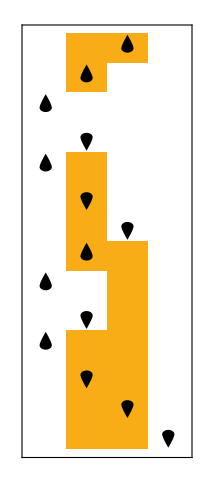
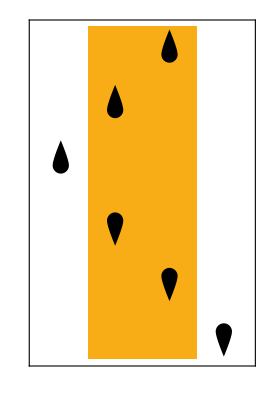
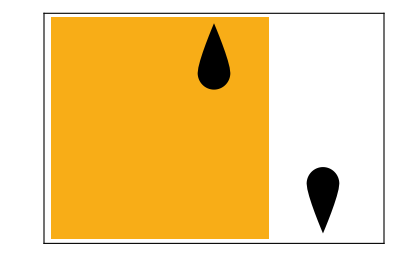

```mathematica
RulePlot[TuringMachine[#1],{{1,IntegerLength[3,2]},{IntegerDigits[3,2],0}},#2]&@@@{{378,13},{1406,5},{3919,1}}
```

This is an example of where the dominating linear TM (378) can be improved significantly (since this function simply does nothing so there exists a TM that solves it in constant time).

Merged runtime plot showing the worse case linear growth rate:

```mathematica
runtimePlot[sorted22[[1,5;;]],{4x},x]
```

-Graphics-

Another group worth pointing out is the 15th function shown below, where there are TM’s that grow linearly and logarithmically, which is another example of where a function’s runtime can be improved, but non-trivially. However, most of the first 40 functions are simply computed by TM’s with the same asymptotic runtime but at different magnitudes, which I hypothesize means that for non-trivial functions, most improvements are going to be reductions by a constant factor instead of in growth rate.

Separate runtime plots for select TM’s in the 4th function:

```mathematica
plotSeparate[sorted22[[4,5;;]]]
```

{2142→{-Graphics-,1},2140→{-Graphics-,1}}

We can also sort by maximum runtime:

```mathematica
sorted22max=SortBy[haltgroups22,-#[[3]]&];
```

Generates plots for the first 36 groups sorted by maximum runtime:

If we generate the separated plots for the first 36 functions (with the function above), observe that most of these functions are only computed by a single or a few TM’s, which may represent problems that are intrinsically difficult to even find a solution for. However, the 29th and 36th functions are interesting in that both are computed by 9 different TM’s, and all of those run in logarithmic time, which represents a more non-trivial function where there are many known solutions but none of them are trivially fast. Strangely, both of these functions trace the same graph...

Runtime plot for the 29th and 36th function, respectively:

```mathematica
Rasterize[runtimePlot[sorted22max[[#,5;;]],{5.8Log2[x+1]},x],ImageSize->Medium]&/@{29,36}
```

{-Graphics-,-Graphics-}

Now we can observe that the peaks of the maximum runtime of function 1 sorted by range and 29 and 36 (and presumably 15) sorted by max occur when the input are around powers of 2 (for function 1, it’s one less than a power of 2). Notice that the numbers represented with a minimum of  bits are between  and , so this brings us to the second way of viewing “input size”: using the length of the input. For each group of inputs represented by some  bits, we take the maximum (or average) of the runtime to get the max/average runtime by input length. This method of evaluating runtime is much cleaner, since the jagged linear function will become a clean exponential, and similarly logarithm to linear.

Compress a list of running times by combining the runtimes of inputs of a certain length with function fn. This defines the compression function in plotSeparate and runtimePlot:

```mathematica
compress[data_List,fn_:Max]:=(fn/@TakeList[data,Prepend[Table[2^k,{k,0,Log2[Length[data]+1]-1}],1]])
```

Plotting by length, we indeed see that the linear function becomes exponential and the logarithm becomes linear. Similarly, taking the average of runtimes for a given length will result in an approximately linear and logarithmic graph like the uncompressed visualization.

```mathematica
Append[plotSeparate[sorted22[[1,5;;]],"Max"][[{1,3,6,7}]],Rasterize[runtimePlot[sorted22[[1,5;;]],{4 2^x},x,"Max"],ImageSize->Medium]]
```

{378→{-Graphics-,2},1406→{-Graphics-,16},3389→{-Graphics-,1},3919→{-Graphics-,193},-Graphics-}

### (2,3) TM’s

We do the same for the (2,3) data:

```mathematica
sorted23=ReverseSortBy[haltgroups23,First];
```

Plot certain runtimes for the function with the largest runtime range:

```mathematica
Append[plotSeparate[sorted23[[1,5;;]],"Max",halts23][[{1,2,-1}]],Rasterize[runtimePlot[sorted23[[1,5;;]],{7.6 2^x},x,"Max",halts23],ImageSize->Medium]]
```

{2085806→{-Graphics-,1},2086095→{-Graphics-,1},2044622→{-Graphics-,1},-Graphics-}

Notice that the first two runtimes unsurprisingly grow exponentially but there also exists a TM that grows linearly without a large constant factor. Fitting the data into an exponential, we get the following equation and R-squared value. This is an elegant example of a problem in P where exponential solutions can be improved to linear.

Fit and R-squared for an exponential:

```mathematica
{Normal[#],#["RSquared"]}&@NonlinearModelFit[compress[First[halts23[2085806]],Max],a(2^(x-0.999)-1),{a,b},x]
```

{7.60028 (-1+2^(-0.999+x)),0.99324}

The anticipated runtimes for an NP-hard function would be where most Turing machines that compute the function compute it near the maximum runtime of all TM’s. This is the opposite of the P problem shown above where there are TM’s that have a high maximum runtime but others with a low maximum runtime. In the (2,3) plot and with the code below, we see that runtime range decreases very quickly, meaning there are a pretty small number of relevant P problems with non-optimal solutions. Below calculates the ratio between the number of P and NP behavior problems:

Gets the number of functions with runtime range ≥400 and the number of functions with min runtime ≥400:

```mathematica
{#1,#2,N[#1/#2]}&@@{Count[haltgroups23[[All,1]],x_/;x>=400],Count[haltgroups23[[All,2]],x_/;x>=400]}
```

{14,59,0.237288}

The second being greater than the first means that there are more problems that seem to be NP-hard and cannot be improved than problems  in P that have superpolynomial algorithms that can be optimized/modified. Since these numbers are very small relative to the 448,334 functions in (2,3) space, I hypothesize means that we need more states and symbols to have a large enough search space to properly represent non-trivial functions, which will be essentially computationally infeasible for exhaustive search.

One last manipulation we can do is to sort the compressed data (by max runtime) by how rapidly they increase. I claim that the following function is a sufficient heuristic for this sort.

```mathematica
Total[Differences[#]]&
```

The outline of the proof is as follows: consider two functions  and  whose growth rate we want to compare. Naturally, we will compare the size of their derivatives. Given a list of values of  to  for some positive integer , we can approximate a table of derivatives at integer values since  (and by MVT  where  takes this value). Therefore a sequence of  for  is given by the differences of successive values of  for , which Differences gives. To compare  and , we can approximate their integral with a Riemann sum and compare them, which is simply  and , respectively, or Total[Differences[Table[h[k],{k,0,n-1}]] for some function . To have cleaner functions, we will compress the sequence before taking the differences.

Group (2,3) TM functions and add a growth rate heuristic:

```mathematica
sorted23leninc=ReverseSortBy[Map[
With[{mm=MinMax[Max[#[[3]]]&/@#],grm=Max[Total[Differences[compress[#[[3]],Max]]]&/@#]},Flatten[{mm[[2]]-mm[[1]],mm,Total[#[[All,2]]],grm,#[[All,1]]}]]&,
GatherBy[Select[haltconfig23,Max[#[[3]]]>=0&],#[[4]]&]
],#[[5]]&];
```

By inspection, exponential growth rate tends to collapse at around the 800th function (which is not a lot considering there are 448334 functions in total), so we sample the first 800 functions and count the ones with small runtime range as NP behavior (≤20 in this case) to get a proportion between functions with P behavior and NP behavior.

Return a pair of {# of P behavior, # of NP behavior}:

```mathematica
{#1,#2,N[#1/#2]}&@@({1,-1}({800,0}-Count[Take[{Length[#]-5,First[#]}&/@sorted23leninc,UpTo[800]],p_/;Last[p]<=20]))
```

{106,694,0.152738}

The above proportion is not too far off the proportion found with runtime range and max runtime (0.237), which suggests that for the TM analog of complexity classes, there are classes harder than P that cannot be reduced to P and have substantially more problems in them (can we say about 5 times more?).

### (3,2) TM’s

We will do something very similar to (2,3) TM’s.

Sort data:

```mathematica
sorted32=ReverseSortBy[haltgroups32,First];
```

Plot select TM’s from the function with the largest runtime range:

```mathematica
Append[plotSeparate[sorted32[[1,5;;]],"Max",halts32][[{1,9,-1}]],Rasterize[runtimePlot[sorted32[[1,5;;]],{8.15 2^x},x,"Max",halts32],ImageSize->Medium]]
```

{654539→{-Graphics-,2},630347→{-Graphics-,4},164661→{-Graphics-,6255},-Graphics-}

When we look for the proportion of functions with P and NP behavior, we reduce the range threshold to 250 because the maximum runtimes and thus runtime ranges for (3,2) TM’s are smaller (there are only 2 functions with runtime range ≥400), and the (3,2) graph in the previous section also decayed faster.

Number of functions with runtime range ≥250 and number of functions with min ≥250:

```mathematica
{#1,#2,N[#1/#2]}&@@{Count[haltgroups32[[All,1]],x_/;x>=250],Count[haltgroups32[[All,2]],x_/;x>=250]}
```

{10,51,0.196078}

Notice how this 0.196 ratio is similar to the (2,3) proportion of 0.237 which serves as more evidence that there are more NP-hard problems that cannot be improved than ones that can. Finally, we can sort by growth rate again to find a more accurate proportion.

Group (3,2) TM functions and add a growth rate heuristic:

```mathematica
sorted32leninc=ReverseSortBy[Map[
With[{mm=MinMax[Max[#[[3]]]&/@#],grm=Max[Total[Differences[compress[#[[3]],Max]]]&/@#]},Flatten[{mm[[2]]-mm[[1]],mm,Total[#[[All,2]]],grm,#[[All,1]]}]]&,
GatherBy[Select[haltconfig32,Max[#[[3]]]>=0&],#[[4]]&]
],#[[5]]&];
```

This time exponential growth rate tends to already collapse at around the 40th function (compared to the 800 for (2,3) TM’s), so we sample only the first 40 functions and count the ones with small runtime range as NP behavior (again with 20 as the range threshold).

Return a pair of {# of P behavior, # of NP behavior}:

```mathematica
{#1,#2,N[#1/#2]}&@@({1,-1}({40,0}-Count[Take[{Length[#]-5,First[#]}&/@sorted32leninc,UpTo[40]],p_/;Last[p]<=20]))
```

{10,30,0.333333}

The above ratio is not that close to the 0.196 ratio we got previously, which I hypothesize is because the first method is more likely to count polynomial/linear functions with a large constant, which is more likely to be eliminated using this method, but regardless, there still seems to be more NP-hard problems than P problems in the (3,2) search space, which is likely to generalize to most  combinations.

### Larger (s,k) TM’s

For (2,4) and (4,2), there are  = 4294967296 machines and for (3,3) there are  machines which is far too many to enumerate, so we take a random sample of 2 million rules and run them. (2,4) was done with

```mathematica
halts24=ParallelMap[getHalts[{#,2,4},6,512]&,DeleteDuplicates[RandomInteger[perm[0,2,4]-1,2000000]]];
```

This data was ran without storing the rules since we did not do any pruning and can simply treat the index as the rule number. We begin by analyzing (2,4) and directly adding the growth rate heuristic.

#### (2,4)

Gather the subset of (4,2) TM’s:

```mathematica
sorted24leninc=ReverseSortBy[Map[
With[{mm=MinMax[Max[#[[2]]]&/@#],grm=Max[Total[Differences[compress[#[[2]],Max]]]&/@#]},Flatten[{Last[mm]-First[mm],mm,Length[#],grm,#[[All,1]]}]]&,
GatherBy[Select[MapIndexed[Prepend[#1,First[#2]]&,halts24],Max[#[[2]]]>=0&],#[[3]]&]
],#[[5]]&];
```

At this point, we will skip the plots and directly calculate the P and ≥NP proportions:

```mathematica
{#1,#2,N[#1/#2]}&@@{Count[sorted24leninc[[All,1]],x_/;x>=200],Count[sorted24leninc[[All,2]],x_/;x>=200]}
```

{6,432,0.0138889}

This is the expected result as mentioned in the previous section that a larger search space means relatively less P problem. Now we calculate this ratio the second way. By inspecting the separated plots (note that in this subsection, we can pass halts24[[#]]& to the halts parameter in plotSeparate), exponential growth tends to collapse at around the 350th function, so we use that threshold to calculate the second ratio:

```mathematica
{#1,#2,N[#1/#2]}&@@({1,-1}({350,0}-Count[Take[{Length[#]-5,First[#]}&/@sorted24leninc,UpTo[350]],p_/;Last[p]<=20]))
```

{8,342,0.0233918}

As predicted, this ratio is again smaller.

#### (4,2)

For (4,2), we have

```mathematica
sorted42leninc=ReverseSortBy[Map[
With[{mm=MinMax[Max[#[[2]]]&/@#],grm=Max[Total[Differences[compress[#[[2]],Max]]]&/@#]},Flatten[{Last[mm]-First[mm],mm,Length[#],grm,#[[All,1]]}]]&,
GatherBy[Select[MapIndexed[Prepend[#1,First[#2]]&,halts42],Max[#[[2]]]>=0&],#[[3]]&]
],#[[5]]&];
```

Calculate the first proportion:

```mathematica
{#1,#2,N[#1/#2]}&@@{Count[sorted42leninc[[All,1]],x_/;x>=400],Count[sorted42leninc[[All,2]],x_/;x>=400]}
```

{8,31,0.258065}

Surprisingly, this number is even higher than the first proportions of (2,3) and (3,2), and I have yet to figure out why this is. Moving to the second proportion with a threshold at 20 (again, by inspection), we have

```mathematica
{#1,#2,N[#1/#2]}&@@({1,-1}({20,0}-Count[Take[{Length[#]-5,First[#]}&/@sorted42leninc,UpTo[20]],p_/;Last[p]<=20]))
```

{6,14,0.428571}

which is an even higher ratio than before.

#### (3,3)

Finally, for (3,3), we have

```mathematica
sorted33leninc=ReverseSortBy[Map[
With[{mm=MinMax[Max[#[[2]]]&/@#],grm=Max[Total[Differences[compress[#[[2]],Max]]]&/@#]},Flatten[{Last[mm]-First[mm],mm,Length[#],grm,#[[All,1]]}]]&,
GatherBy[Select[MapIndexed[Prepend[#1,First[#2]]&,halts33],Max[#[[2]]]>=0&],#[[3]]&]
],#[[5]]&];
```

Calculate the first proportion:

```mathematica
{#1,#2,N[#1/#2]}&@@{Count[sorted33leninc[[All,1]],x_/;x>=200],Count[sorted33leninc[[All,2]],x_/;x>=200]}
```

{16,595,0.0268908}

The growth rates for (3,3) are less clean and it becomes ambiguous where to place a threshold, so we will use 200 as an approximation.

Calculate the second proportion:

```mathematica
{#1,#2,N[#1/#2]}&@@({1,-1}({200,0}-Count[Take[{Length[#]-5,First[#]}&/@sorted33leninc,UpTo[200]],p_/;Last[p]<=10]))
```

{2,198,0.010101}

This number as well as the previous ratio is not much different from the ratios of (2,4), which could be an error in the data or an implication of a rate of slowdown. However, we cannot disregard the (4,2) outlier, which may be an indication that something more complicated is going on or the sampling method is incorrect. Note also that from  to  is a factor of 2000, while  to  is a factor of 50, more than an order of magnitude less.

## Summary of Conclusions

To address the title of this essay, the similarity between the shapes of the minimum and maximum runtime graphs indicates that functions with a bad worse-case running time will also have a relatively worse best-case running time, and fast minimum runtimes will also have faster maximum runtimes. If we view these functions as algorithms, we hypothesize that problems solved with slower unoptimized algorithms will also likely be solved with slower optimal algorithms if we look at the space of all problems. Of course this is not always true: sorting algorithms are one example where there exists a vast pool of algorithms with a large range of runtimes. However, that the runtime range in all our plots decrease very quickly in the set of all rule groups (similar to ), where the left represents the rare case where runtime can be significantly improved (e.g. sorting). Sorting the data by maximum runtime, we can also observe that there are occasional drops in minimum runtime, yet most of the time they are identical. I believe that the small section of large runtime range represents a subset of P problems which can be solved both quickly and very slowly. The gradual convergence of minimum and maximum runtime could be analogous to the runtime of the best possible algorithm approaching brute-force. 

This conclusion is not without flaw, however, since P and NP are not the only complexity classes. Without specific comparisons between the complexity classes, my interpretation would be equally valid if we took P to equal NP and claim that the number of NP problems is significantly smaller than the number of problems harder than NP, which would imply that the quick convergence of runtimes is because there are so many problems so much harder than NP problems. This applies to conclusions made from both the runtime plots and the ratios calculated in the previous section.

Looking specifically at individual runtime plots, we notice fundamentally that the function space given by any  TM always contains functions that run in exponential time, and only a small portion of these have TM’s that improve runtime to subexponential. Those that have read NKS particularly carefully know that rule 445 for  adds 1 to the number on the tape. This rule number is inherently tied to how we encode and decode values on the tape. By alternatively treating the input as the length of the starting values on the tape, we essentially redefine what each rule means because our encoding/decoding method is different, but, crucially, equally valid.

We have yet to calculate the ratio for (2,2) TM’s. The first method of using runtime range and minimum runtime is pretty ineffective since the runtimes of (2,2) TM’s is pretty low, so we skip directly to the second method

```mathematica
sorted22leninc=ReverseSortBy[Map[
With[{mm=MinMax[Max[#[[3]]]&/@#],grm=Max[Total[Differences[compress[#[[3]],Max]]]&/@#]},Flatten[{mm[[2]]-mm[[1]],mm,Total[#[[All,2]]],grm,#[[All,1]]}]]&,
GatherBy[Select[haltconfig,Max[#[[3]]]>=0&],#[[4]]&]
],#[[5]]&];
```

Without doing any calculation, inspecting the plots of the first 5 functions with exponential runtime suggests that there are no problems in the (2,2) space with NP behavior, since the exponential TM’s can be improved to constant or linear time.

Generate the longest and shortest runtime plots for the first 5 functions:

```mathematica
Table[i->plotSeparate[sorted22leninc[[i,6;;]],"Max"][[{1,-1}]],{i,5}]//Column
```

The one conclusion we made from looking at the proportion between functions with P and NP behavior is that for a larger problem space, there is more potential for there to be hard problems, and the number of these problems that can be improved decreases, but potentially decreases slower as  and  increase. This is clearly supported by the lack of NP problems in the (2,2) search space.

## Future Directions

Further analyze the TM runtimes and use different runtime schemes to find more general patterns not specific to a single runtime scheme

Optimize current implementations and add more advanced optimization

Investigate the ratio increase of (4,2) TM’s

Generate, visualize, and analyze data for larger  pairs

Extend to nondeterministic Turing machines to try to resolve the issue brought up in the previous section of not knowing the relative cardinality of P, NP, EXPTIME, etc.

## Acknowledgements

I would like to thank my mentor Felipe Amorim for supporting me throughout this project, keeping me on track, and helping me organize and implement my ideas. I would also like to thank my teaching assistant Gregory Roudenko for inspiring the methods I used for code optimization, mentor Shenghui Yang for explaining code compilation and approaches to code optimization, and the program directors Rory Foulger, Megan Davis, and Eryn Gillam for accepting me into WSRP. Finally, I would like to thank Dr. Stephen Wolfram for giving me this illuminating project and its motivation as an unconventional approach to complexity theory.

## References

Ariel (https://cs.stackexchange.com/users/27055/ariel), Given two total Turing machines, is it undecidable problem to detect whether they give the same output on all inputs?, URL (version: 2015-08-30): https://cs.stackexchange.com/q/45687

Manlio (https://math.stackexchange.com/users/22701/manlio), How are weakly universal Turing machines actually defined?, URL (version: 2020-04-22): https://math.stackexchange.com/q/3634837

Weisstein, Eric W. “Turing Machine.” From MathWorld--A Wolfram Resource. https://mathworld.wolfram.com/TuringMachine.html

Wikipedia contributors. (2025, June 30). Automata theory. In Wikipedia, The Free Encyclopedia. Retrieved 15:56, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Automata_theory&oldid=1298074772

Wikipedia contributors. (2025, April 14). DFA minimization. In Wikipedia, The Free Encyclopedia. Retrieved 15:59, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=DFA_minimization&oldid=1285525404

Wikipedia contributors. (2025, June 12). Halting problem. In Wikipedia, The Free Encyclopedia. Retrieved 21:23, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Halting_problem&oldid=1295203495

Wikipedia contributors. (2025, March 18). Rice’s theorem. In Wikipedia, The Free Encyclopedia. Retrieved 15:58, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Rice%27s_theorem&oldid=1281112418

Wikipedia contributors. (2025, June 24). Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved July 2, 2025, from https://en.wikipedia.org/w/index.php?title=Turing_machine&oldid=1297184647

Wikipedia contributors. (2025, March 17). Universal Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved 15:55, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Universal_Turing_machine&oldid=1281033475

Wolfram, S. (2002). A New Kind of Science. Retrieved from https://www.wolframscience.com